{43.2,432.,460.8,374.4,230.4,201.6,201.6,187.2,172.8,187.2,201.6}

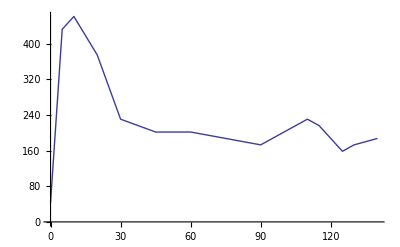

1.3

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

1.05

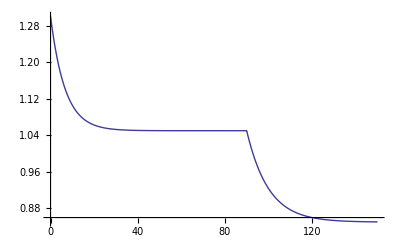

Schw2-1c.xls

3

```mathematica
(*p1*)
texpLong={0,5,10,20,30,45,60,75,90,95,100,105,110,115,120,125,130,140};
texp=Take[texpLong,11];
PexpPmolLong={1.5,15,16,13,8,7,7,6.5,6,6.5,7,7.5,8,7.5,6.5,5.5,6,6.5};
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11];
Pexp=3*9.6*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
ca0=1.3
sc=NDSolve[{Ca'[t]==Piecewise[{{0.15*(1.05-Ca[t]),t<90},{0.1*(0.85-Ca[t]),90≤t}}],Ca[0]==ca0},Ca,{t,0,150}]
ca1=Ca[75]/.sc[[1]]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw2-1c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
SVol=3
```

```mathematica
ClearAll[kv,kdeg,beta,gamma,kd,m,sse,Ca,P,bP,a,b];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.15*(1.05-Ca[t]),t<90},{0.1*(0.85-Ca[t]),90≤t}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+b*ca0-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m]},{kv,35},{a,0.05},{b,0.05},{beta,0.2},{gamma,0.2},{kd,1.15},{m,20},Method->Newton]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3825.85,{kv→33.2504,a→-0.0968519,b→0.0810749,beta→0.122817,gamma→0.230403,kd→1.29616,m→20.622}}

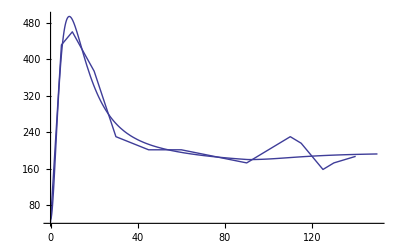

Schw2-1a.xls

3825.85

Schw2-1b.xls

0.975595

0.946548

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];

s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),Ca'[t]==Piecewise[{{0.15*(1.05-Ca[t]),t<90},{0.1*(0.85-Ca[t]),90≤t}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]

T2=Table[{t,P[t]/.s[[1]]},{t,0,150,1}];
Export["Schw2-1a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]

T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-1b.xls",%]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

{1.5,17,18,12,7,6,5.5,5.5,5,7,7.5}

{43.2,489.6,518.4,345.6,201.6,172.8,158.4,158.4,144.,201.6,216.}

1.3

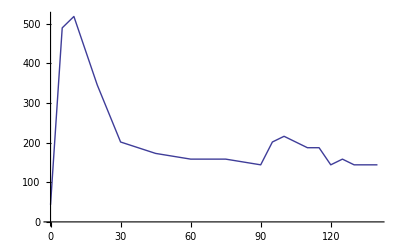

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

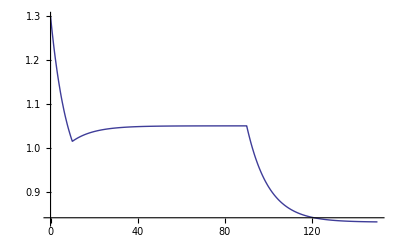

Schw2-2c.xls

```mathematica
(*p2*)
texpLong={0,5,10,20,30,45,60,75,90,95,100,105,110,115,120,125,130,140};
texp=Take[texpLong,11];
PexpPmolLong={1.5,17,18,12,7,6,5.5,5.5,5,7,7.5,7,6.5,6.5,5,5.5,5,5};
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11]
Pexp=3*9.6*PexpPmol
ca0=1.3
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
sc=NDSolve[{Ca'[t]==Piecewise[{{0.125*(0.9-Ca[t]),t<10},{0.1*(1.05-Ca[t]),10<=t<90},{0.1*(0.83-Ca[t]),90≤t}}],Ca[0]==ca0},Ca,{t,0,150}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw2-2c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
```

```mathematica
ClearAll[kv,kdeg,beta,gamma,kd,m,sse,Ca,P,bP,a,b];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.125*(0.9-Ca[t]),t<10},{0.1*(1.05-Ca[t]),10<=t<90},{0.1*(0.83-Ca[t]),90≤t}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+b*ca0-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
bP=bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m]},{kv,35},{a,0.05},{b,0.05},{beta,0.2},{gamma,0.2},{kd,1.15},{m,20},Method->Newton]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{7449.01,{kv→35.6201,a→-0.0281684,b→0.0292041,beta→0.134819,gamma→0.210459,kd→1.26705,m→19.9117}}

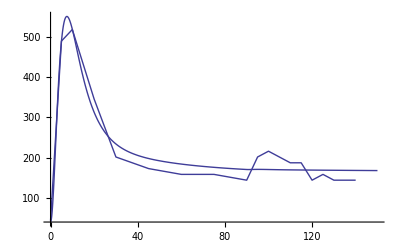

Schw2-2a.xls

7449.01

Schw2-2b.xls

0.96618

0.955512

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];

s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),Ca'[t]==Piecewise[{{0.125*(0.9-Ca[t]),t<10},{0.1*(1.05-Ca[t]),10<=t<90},{0.1*(0.83-Ca[t]),90≤t}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]

T2=Table[{t,P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-2a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-2b.xls",%]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

{2,12,14,8,5,4.5,3.5,3.25,4.5,6.5,6}

{57.6,345.6,403.2,230.4,144.,129.6,100.8,93.6,129.6,187.2,172.8}

1.33

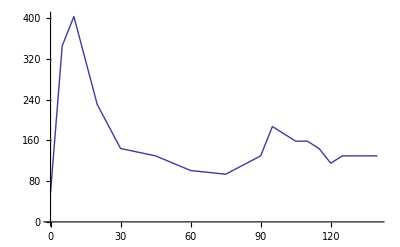

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

Schw2-3c.xls

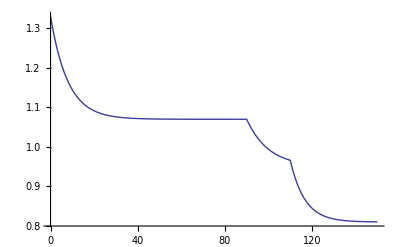

```mathematica
(*p3*)
texpLong={0,5,10,20,30,45,60,75,90,95,100,105,110,115,120,125,130,140};
texp=Take[texpLong,11];
PexpPmolLong={2,12,14,8,5,4.5,3.5,3.25,4.5,6.5,6,5.5,5.5,5,4,4.5,4.5,4.5};
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,11]
Pexp=3*9.6*PexpPmol
ca0=1.33
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
sc=NDSolve[{Ca'[t]==Piecewise[{{0.125*(1.07-Ca[t]),t<90},{0.1*(0.95-Ca[t]),90≤t<110},{0.15*(0.81-Ca[t]),110≤t<150}}],Ca[0]==ca0},Ca,{t,0,150}]
T1=Table[{t,Ca[t]/.sc[[1]]},{t,0,150,2.5}];
Export["Schw2-3c.xls",%]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All]
ClearAll[Ca,sc,sse,bP,V]
```

```mathematica
ClearAll[kv,kdeg,beta,gamma,kd,m,sse,Ca,P,bP,a,b];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.125*(1.07-Ca[t]),t<90},{0.1*(0.95-Ca[t]),90≤t<110},{0.15*(0.81-Ca[t]),110≤t<150}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+b*ca0-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
bP=bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m]},{kv,36},{a,-0.06},{b,0.05},{beta,0.2},{gamma,0.2},{kd,1.15},{m,20},Method->Newton]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9088.7,{kv→32.4135,a→0.138398,b→-0.0959696,beta→0.236022,gamma→0.299988,kd→1.24971,m→18.9461}}

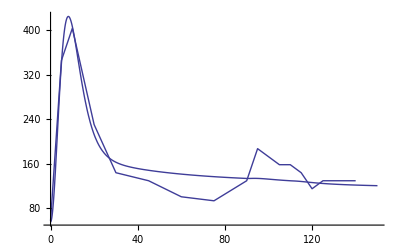

Schw2-3a.xls

9088.7

Schw2-3c.xls

0.920942

0.91037

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];

s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),Ca'[t]==Piecewise[{{0.125*(1.07-Ca[t]),t<90},{0.1*(0.95-Ca[t]),90≤t<110},{0.15*(0.81-Ca[t]),110≤t<150}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]

T2=Table[{t,P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-3a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-3c.xls",%]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```

{1.5,15,18,13,8,7,6,5.5}

{43.2,432.,518.4,374.4,230.4,201.6,172.8,158.4}

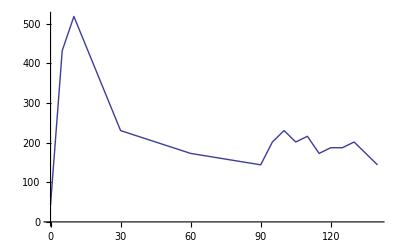

{{Ca→InterpolatingFunction[{{0.,150.}},<>]}}

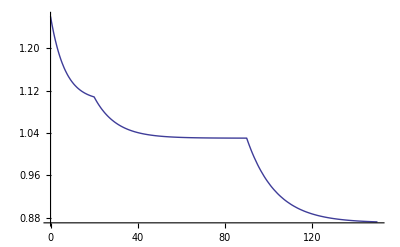

Schw2-4c.xls

```mathematica
(*p4*)
texpLong={0,5,10,20,30,45,60,75,90,95,100,105,110,115,120,125,130,140};
texp=Take[texpLong,8];
PexpPmolLong={1.5,15,18,13,8,7,6,5.5,5,7,8,7,7.5,6,6.5,6.5,7,5};
PexpLong=3*9.6*PexpPmolLong;
PexpPmol=Take[PexpPmolLong,8]
Pexp=3*9.6*PexpPmol
ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]
sc=NDSolve[{Ca'[t]==Piecewise[{{0.15*(1.1-Ca[t]),0<=t<20},{0.1*(1.03-Ca[t]),20<=t<90},{0.075*(0.87-Ca[t]),90≤t}}],Ca[0]==1.26},Ca,{t,0,150}]
Plot[Evaluate[Ca[t]/.sc],{t,0,150},PlotRange->All]
T1=Table[{Ca[t]/.sc[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-4c.xls",%]
ClearAll[Ca,sc,sse,bP,V]
```

```mathematica
ClearAll[kv,kdeg,beta,gamma,kd,m,sse,Ca,P,bP,a,b];
sse[kv_?NumberQ,a_?NumberQ,b_?NumberQ,beta_?NumberQ,gamma_?NumberQ,kd_?NumberQ,m_?NumberQ]:=Block[{sol,P},sol=NDSolve[{P'[t]==(beta-(gamma*Ca[t]^m/(Ca[t]^m+kd^m)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kv*(beta-gamma*ca0^m/(ca0^m+kd^m))/(a+b*ca0+beta-gamma*ca0^m/(ca0^m+kd^m)),Ca'[t]==Piecewise[{{0.15*(1.1-Ca[t]),0<=t<20},{0.1*(1.03-Ca[t]),20<=t<90},{0.075*(0.87-Ca[t]),90≤t}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kv-(a+b*Ca[t]+beta-gamma*Ca[t]^m/(Ca[t]^m+kd^m))*V[t],V[0]==kv/((beta+a+b*ca0-gamma*(ca0^m)/(ca0^m+kd^m)))},{P,Ca,V,EP},{t,0,100}][[1]];
Apply[Plus,(Pexp-(P[t]/.sol/.t->texp))^2]]
bP=FindMinimum[{sse[kv,a,b,beta,gamma,kd,m]},{kv,30},{a,-0.025},{b,0.022},{beta,0.22},{gamma,0.2},{kd,1.175},{m,20},Method->Newton]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{1424.09,{kv→34.3689,a→0.093829,b→-0.0655169,beta→0.0985112,gamma→0.153046,kd→1.29903,m→21.9802}}

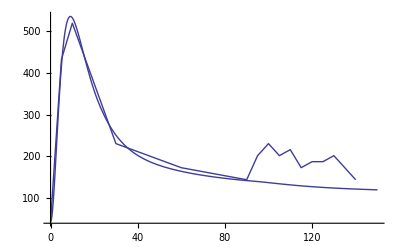

Schw2-4a.xls

1424.09

Schw2-4b.xls

0.992014

0.80542

```mathematica
kves=kv/.bP[[2,1]];
aa=a/.bP[[2,2]];
bb=b/.bP[[2,3]];
bet=beta/.bP[[2,4]];
gam=gamma/.bP[[2,5]];
k=kd/.bP[[2,6]];
mm=m/.bP[[2,7]];

s=NDSolve[{P'[t]==(bet-(gam*Ca[t]^mm/(Ca[t]^mm+k^mm)))*V[t]-0.6613*P[t]/3-EP'[t],P[0]==4.53652*kves*(bet-gam*ca0^mm/(ca0^mm+k^mm))/(aa+bb*ca0+bet-gam*ca0^mm/(ca0^mm+k^mm)),Ca'[t]==Piecewise[{{0.15*(1.1-Ca[t]),0<=t<20},{0.1*(1.03-Ca[t]),20<=t<90},{0.075*(0.87-Ca[t]),90≤t}}],Ca[0]==ca0,EP'[t]==0.5*(P[t]/SVol-EP[t]/11),EP[0]==(11/SVol)*PexpLong[[1]],V'[t]==kves-(aa+bb*Ca[t]+bet-gam*Ca[t]^mm/(Ca[t]^mm+k^mm))*V[t],V[0]==kves/((bet+aa+bb*ca0-gam*(ca0^mm)/(ca0^mm+k^mm)))},{P,Ca,V,EP},{t,0,150}];
Show[Plot[Evaluate[P[t]/.s],{t,0,150},PlotRange->All],ListPlot[Transpose[{texpLong,PexpLong}],Joined->True]]

T2=Table[{t,P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-4a.xls",%]

ParametricPlot[Evaluate[{Ca[t],P[t]/3}/.s][[1]],{t,0,150},AspectRatio->0.75];
Apply[Plus,(Pexp-(P[t]/.s/.t->texp)[[1]])^2]
T3=Table[{Ca[t]/.s[[1]],P[t]/.s[[1]]},{t,0,150,2.5}];
Export["Schw2-4b.xls",%]

Pbar=Mean[PexpLong];
PbarShort=Mean[Pexp];
SStotShort=Total[(Pexp-PbarShort)^2];
SStot=Total[(PexpLong-Pbar)^2];
SSerrShort=Total[(Pexp-(P[t]/.s/.t->texp)[[1]])^2];
SSerr=Total[(PexpLong-(P[t]/.s/.t->texpLong)[[1]])^2];
r2Short=1-SSerrShort/SStotShort
r2=1-SSerr/SStot
```